# Nanobody fits (L=80μm)

## Read data in

```mathematica
SetDirectory["/Users/hadjivz/Dropbox/Mac/Desktop/CodeOnline/Nanobody/L80/"];
files=FileNames["dat*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
dat=Table[Import[files[[f]],"Table"],{f,1,Length[files]}]//N;
```

## Define model and fit simultaneously

From A, B, p to ks functions

```mathematica
fko := Function[{p,B, A}, p - p^2 B / (p B + A)]
fkN := Function[{p,B, A},(p B + A)]
fkr := Function[{p,B, A},p^2 B / (p B + A)]
```

Format data for simultaneous fit

```mathematica
datIndexed = Table[Table[{dat[[i,j,1]], i, dat[[i,j,2]]}, {j,1,Length[dat[[i]]]}], {i,1,Length[dat]}];
```

```mathematica
(*fitted initial intensity point (at t=0) cannot be higher than first measurement at t0>0*)
ciMax=Table[dat[[i,1,2]], {i,1,Length[dat]}];
```

Sample length up to t=4500s across experiments

```mathematica
maxT = 4500;
dat1=Table[Table[If[dat[[j,i,1]]<maxT, dat[[j,i]]], {i, 1, Length[dat[[j]]]}], {j,1,Length[dat]}];
dat2=Table[DeleteCases[dat1[[j]], Null], {j,1,Length[dat1]}];
datIndexed = Table[Table[{dat2[[i,j,1]], i, dat2[[i,j,2]]}, {j,1,Length[dat2[[i]]]}], {i,1,Length[dat2]}];
```

Fits (simultaneous)

```mathematica
modelc1:=c1(1+A t+B(1-Exp[-p t]));
modelc2:=c2(1+A t+B(1-Exp[-p t]));
modelc3:=c3(1+A t+B(1-Exp[-p t]));
modelc4:=c4(1+A t+B(1-Exp[-p t]));
modelc5:=c5(1+A t+B(1-Exp[-p t]));
modelc6:=c6(1+A t+B(1-Exp[-p t]));
modelc7:=c7(1+A t+B(1-Exp[-p t]));
modelc8:=c8(1+A t+B(1-Exp[-p t]));
modelc9:=c9(1+A t+B(1-Exp[-p t]));
modelc10:=c10(1+A t+B(1-Exp[-p t]));
modelc11:=c11(1+A t+B(1-Exp[-p t]));

modelSimultaneous[index_]:=KroneckerDelta[index-1]*modelc1+KroneckerDelta[index-2]*modelc2+KroneckerDelta[index-3]*modelc3+KroneckerDelta[index-4]*modelc4+KroneckerDelta[index-5]*modelc5+KroneckerDelta[index-6]*modelc6+KroneckerDelta[index-7]*modelc7+KroneckerDelta[index-8]*modelc8+KroneckerDelta[index-9]*modelc9+KroneckerDelta[index-10]*modelc10+KroneckerDelta[index-11]*modelc11;
```

```mathematica
ciStart = 0.1;
fitsSimultaneous=NonlinearModelFit[Flatten[datIndexed,1],{modelSimultaneous[indexi],A>0, B>0 , 0.1>p>0,
 ciMax[[1]]>c1>0,
 ciMax[[2]]>c2>0,
 ciMax[[3]]>c3>0,
 ciMax[[4]]>c4>0,
 ciMax[[5]]>c5>0,
 ciMax[[6]]>c6>0,
 ciMax[[7]]>c7>0,
 ciMax[[8]]>c8>0,
 ciMax[[9]]>c9>0,
ciMax[[10]]>c10>0,
 ciMax[[11]]>c11>0
},{{c1,ciStart},{c2,ciStart},{c3,ciStart},{c4,ciStart},{c5,ciStart},{c6,ciStart},{c7,ciStart},{c8,ciStart},{c9,ciStart},{c10,ciStart},{c11,ciStart},{A, 0.1}, {B,30}, {p,0.01}},{t,indexi},VarianceEstimatorFunction->(Mean[Abs[#]]&)];
```

Translate (A, B, p) from fit to (ko, kN, kr) and plot fitted curves with experimental data

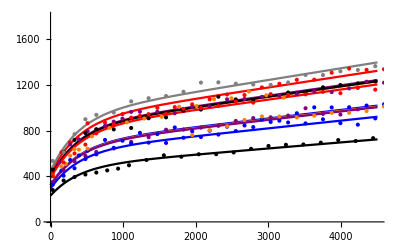

```mathematica
imin=1;
imax=11;
maxt = maxT;
maxy=1800;
imin=1;
imax=11;
Show[Plot[Evaluate@Table[modelSimultaneous[i]/.fitsSimultaneous["BestFitParameters"],{i,imin,imax}],{t,0,maxt},PlotStyle->{Orange, Red, Purple, Blue, Black, Gray},PlotRange->{{0,6000},{0,maxy}}],
ListPlot[Table[dat[[i]], {i,imin,imax}],PlotStyle->{Orange, Red, Purple, Blue, Black, Gray}],TicksStyle->Directive[Black, 14], PlotRange->{{0,maxT},{0,maxy}}]
```

```mathematica
ko=fko[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kN=fkN[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kr=fkr[p,B,A]/.fitsSimultaneous["BestFitParameters"]
```

0.000193751

0.00309817

0.00240721

```mathematica
fitsSimultaneous["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c1 | 392.098 | 1.88869 | 207.603 | 3.66875×10^-242
c2 | 421.497 | 2.00478 | 210.246 | 2.70726×10^-243
c3 | 395.616 | 1.9048 | 207.694 | 3.35163×10^-242
c4 | 324.355 | 1.56887 | 206.745 | 8.6151×10^-242
c5 | 392.622 | 1.87922 | 208.928 | 9.89049×10^-243
c6 | 444.992 | 2.1176 | 210.14 | 3.00584×10^-243
c7 | 321.455 | 1.56545 | 205.344 | 3.49553×10^-241
c8 | 383.463 | 1.83768 | 208.667 | 1.28026×10^-242
c9 | 319.99 | 1.55303 | 206.042 | 1.7383×10^-241
c10 | 293.319 | 1.43247 | 204.765 | 6.25484×10^-241
c11 | 230.262 | 1.15491 | 199.377 | 1.51848×10^-238
A | 0.000230789 | 1.93003×10^-6 | 119.578 | 5.36109×10^-193
B | 1.10243 | 0.0095228 | 115.768 | 3.96429×10^-190
p | 0.00260096 | 0.0000281085 | 92.5329 | 2.26176×10^-170

Calculate s.e.m. for ko, kN, kr

```mathematica
(*variance for A, B, p from fits above*)
LOP80={varp -> (0.000022649223632176612)^2, varA -> (0.000001517)^2, varB ->(0.010338262793552612)^2, p->0.002403760710819817,A->0.00020951618356541564, B->1.2073821084789627};
ParsNow=LOP80;

(*Error propagation formula for kN*)
VarkN = varp varB + varp B^2 + varB p^2 + varA;
fskN=(D[(A+B p),A]^2 varA + D[(A+B p),B]^2 varB +  D[(A+B p),p]^2 varp );
semkn=Sqrt[fskN/.ParsNow]
```

0.0000369821

```mathematica
(*Error propagation formula for kr*)
fskr=(D[p^2 B/(p B + A),A]^2 varA + D[p^2 B/(p B + A),B]^2 varB +  D[p^2 B/(p B + A),p]^2 varp );
semkr=Sqrt[fskr/.ParsNow]
```

0.00002261

```mathematica
(*Error propagation formula for ko*)
Varko = varp + varkr;
semko=Sqrt[Varko/.{varkr->fskr}/.ParsNow]
```

0.0000320031